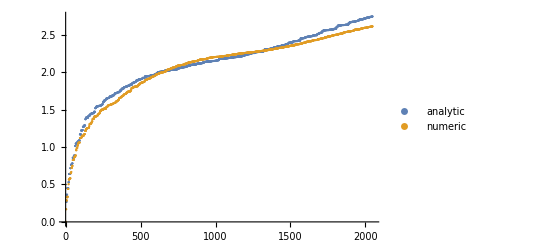

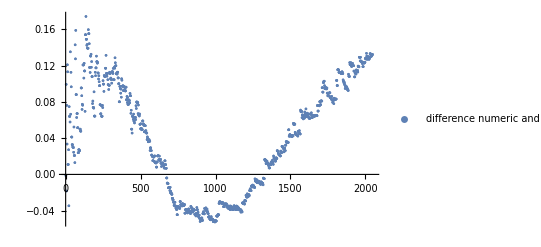

```mathematica
Lx=32;
Ly=32;
fieldsize=32;
n=32;
d=100/100;
γ[kx_,ky_]:=1/2*(Cos[kx]+Cos[ky]);
A[kx_,ky_,δ_]=0.25*((4-2*γ[kx,ky])*0.5(Cos[δ]+1)+2*γ[kx,ky]+(2-Cos[kx])*Sin[δ]*Tan[δ]);
B[kx_,ky_,δ_]=0.25*(2*(γ[kx,ky]*0.5*(1+Cos[δ])+γ[kx,ky]+0.5Cos[kx]*Sin[δ]*Tan[δ]));
ϵ[kx_,ky_,δ_]=2*Sqrt[A[kx,ky,ArcTan[δ]]^2-B[kx,ky,ArcTan[δ]]^2];
SetDirectory[NotebookDirectory[]];
numeric=Import["Bogoliubov/eigenvalueD"<>ToString[d*100]<>"cJxsize"<>ToString[Lx]<>"ysize"<>ToString[Ly]<>"fieldsize"<>ToString[fieldsize]<>".dat","Data"];
list=Table[{ϵ[2*π*i/n,2*π*j/n,d],ϵ[2*π*i/n,2*π*j/n,d]},{i,0,n-1},{j,0,n-1}];
ListPlot[{Sort[Flatten[list]],Sort[Flatten[Abs[numeric]]]},PlotLegends->{"analytic","numeric"}]
ListPlot[{Sort[Flatten[list]]-Sort[Flatten[Abs[numeric]]]},PlotLegends->{"difference numeric and analytic"}]
```

```mathematica
Sort[Flatten[numeric]]
```

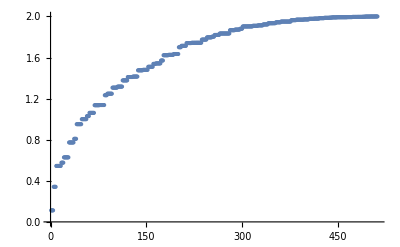

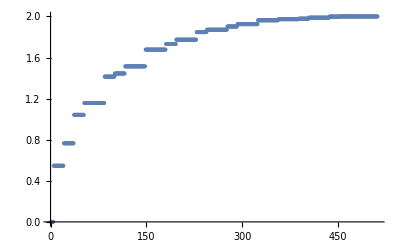

```mathematica
ListPlot[Sort[Flatten[Abs[numeric]]],PlotRange->All]
ListPlot[Sort[Flatten[list]]]
```